# Programming HHLineHistogram

## Inspiration

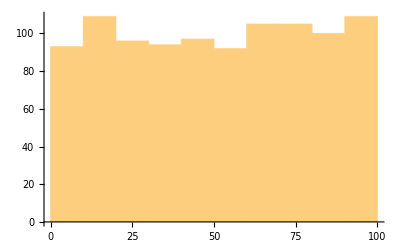

```mathematica
Histogram[RandomReal[{1,100},1000]]
```

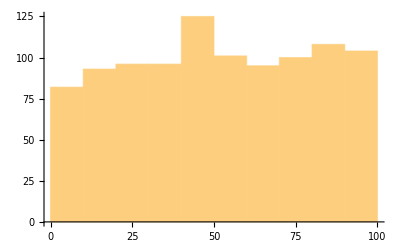

```mathematica
Histogram[RandomReal[{1,100},1000], ChartStyle->EdgeForm[Thick]]
```

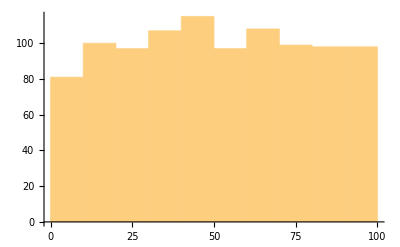

```mathematica
Histogram[RandomReal[{1,100},1000],Automatic, ChartStyle->EdgeForm[Thick]]
```

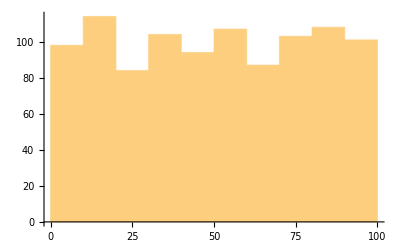

```mathematica
Histogram[RandomReal[{1,100},1000],Automatic,Automatic, ChartStyle->EdgeForm[Thick]]
```

```mathematica
(*https://stackoverflow.com/questions/8839847/histogram-without-vertical-lines-in-mathematica*)
```

```mathematica
histPlot[data_,bins_,color_: Blue]:=Module[{countBorder=Partition[Riffle[Riffle[#1,#1[[2;;]]],Riffle[#2,#2]],2]&@@HistogramList[data,bins,"PDF"]},ListLinePlot[countBorder,PlotStyle->color]]
```

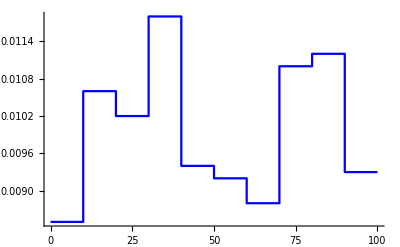

```mathematica
histPlot[RandomReal[{1,100},1000], {10}]
```

## Programming

```mathematica
<<HokahokaW`
```

HokahokaW`
Fri 22 Dec 2017 11:43:35     [Mathematica: 11.2.0 for Microsoft Windows (64-bit) (September 11, 2017)]
     Artifact info as of: Sat 13 May 2017 11:18:54
     Local repo path:   C:\prog\_w\HokahokaW\.git
     Current branch [hash]:  master [157eae2b85e37292b25f4351e2d6c81ab817371e]
     Remote:  origin (https://ktakagaki@github.com/ktakagaki/HokahokaW.git)

```mathematica
Options[HHLineHistogram]= HHJoinOptionLists[
	Options[ListLinePlot],
	{}
];
```

```mathematica
HHLineHistogram[data_/;HHRaggedArrayDepth[data]==1, bspec_:Automatic, hspec_:Automatic, opts:OptionsPattern[] ]:=
	HHLineHistogramImpl[HistogramList[data,bspec,hspec]];
      
HHLineHistogram[data_/;HHRaggedArrayDepth[data]==2, bspec_:Automatic, hspec_:Automatic, opts:OptionsPattern[] ]:=
Block[
	{realOptionList = HHPlotStyleTable[ OptionValue[PlotStyle], {Length[data]}]}, 
	(*Print[realOptionList];*)
		MapThread[
			HHLineHistogramImpl[HistogramList[#1, bspec, hspec], PlotStyle->#2]&, {data, realOptionList}
		]
];
```

```mathematica
HHLineHistogram[args___] := Message[HHLineHistogram::invalidArgs, {args}];
```

### Implementation

```mathematica
Options[HHLineHistogramImpl]= HHJoinOptionLists[
	Options[ListLinePlot],
	{}
];
```

```mathematica
HHLineHistogramImpl[histogramList_/;HHRaggedArrayDepth[histogramList]==2, opts:OptionsPattern[] ]:=
Module[{countBorder=Partition[Riffle[Riffle[#1,#1[[2;;]]],Riffle[#2,#2]],2]&@@histogramList},
	ListLinePlot[countBorder, Sequence@@FilterRules[{opts}, ListLinePlot]]
];
```

```mathematica
HHLineHistogramImpl[args___] := Message[HHLineHistogramImpl::invalidArgs, {args}];
```

## Function Testing

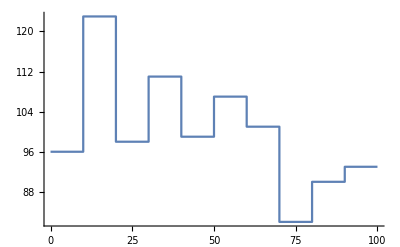

```mathematica
HHLineHistogram[RandomReal[{1,100},1000],{10}]
```

```mathematica
Remove[HHLineHistogram]
```

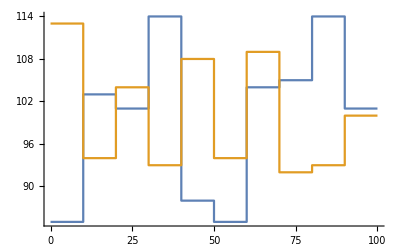

```mathematica
HHLineHistogram[
{RandomReal[{1,100},1000],RandomReal[{1,100},1000]},{10}, PlotRange->All
]
```